```mathematica
PEuler[3 uhat + 2utilde]
```

3 PEuler[uhat]

```mathematica
PEuler[LEuler[3uhat+2utilde]]
```

3 PEuler[LEuler[uhat]]+2 PEuler[LEuler[utilde]]

```mathematica
u
```

uhat+utilde

```mathematica
PEuler[u]
```

uhat

```mathematica
Ck[0,15]
```

0

```mathematica
PSimplify[CExpand[PEuler[LEuler[QEuler[LEuler[u]]]]]]
```

PSimplify[Chat[uhat,Ctilde[uhat,uhat]]-Chat[Chat[uhat,uhat],uhat]+Chat[Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]-Ctilde[uhat,Chat[uhat,uhat]]+Ctilde[uhat,Chat[uhat,uhat]+Ctilde[uhat,uhat]]-Ctilde[Chat[uhat,uhat],uhat]+Ctilde[Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]]

```mathematica
u
```

uhat+utilde

```mathematica
Plus[Ck[a,b],Ck[b,a]]:=Dk[a_,b_]
```

$Failed

```mathematica
PSimplify[a+b+c]
```

a+b+c

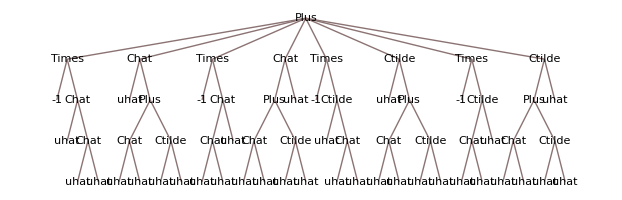

```mathematica
TreeForm[CExpand[PEuler[LEuler[QEuler[LEuler[u]]]]]]
```

```mathematica
PSimplify[Chat[3Ctilde[v,z],w]]
```

3 Chat[Ctilde[v,z],w]

```mathematica
QEuler[2u+3uhat+5utilde]
```

2 u-2 uhat+5 utilde

```mathematica
Dk[3x,0]
```

0

```mathematica
LEuler[Chat[v,v]]
```

Dhat[v,LEuler[v]]

```mathematica
DCollapse[3Ck[a,b]+Ck[3b,a]]
```

3 Dk[a,b]

-2 Dk[uhat,Dhat[uhat,Chat[uhat,uhat]]]+Dk[uhat,Dhat[uhat,Ck[uhat,uhat]]]+2 Dk[uhat,Dk[uhat,Chat[uhat,uhat]]]-Dk[uhat,Dk[uhat,Ck[uhat,uhat]]]-Dk[Chat[uhat,uhat],Chat[uhat,uhat]]+2 Dk[Chat[uhat,uhat],Ck[uhat,uhat]]-Dk[Ck[uhat,uhat],Ck[uhat,uhat]]

```mathematica
FullForm[Expand[P[L[Q[L[u]]]]/.{P->PEuler,Q->QEuler,L->LEuler}]]
```

Plus[Times[-1,Ck[uhat,Chat[uhat,uhat]]],Ck[uhat,Ck[uhat,uhat]],Times[-1,Ck[Chat[uhat,uhat],uhat]],Ck[Ck[uhat,uhat],uhat]]

```mathematica
Dify[Ck[uhat,Ck[uhat,uhat]]+Ck[Ck[uhat,uhat],uhat]]
```

Dify[Ck[uhat,Ck[uhat,uhat]]+Ck[Ck[uhat,uhat],uhat]]

```mathematica
Simplify[Dify[Expand[P[L[Q[L[u]]]]/.{P->PEuler,Q->QEuler,L->LEuler}]]]
```

-Dk[uhat,Chat[uhat,uhat]]+Dk[uhat,Ck[uhat,uhat]]

```mathematica
Expand[P[L[Q[L[u]]]]]/.{P->PEuler,Q->QEuler,L->LEuler}
```

-Ck[uhat,Chat[uhat,uhat]]+Ck[uhat,Ck[uhat,uhat]]-Ck[Chat[uhat,uhat],uhat]+Ck[Ck[uhat,uhat],uhat]

```mathematica
Q[L[u]]/.{P->PEuler,Q->QEuler,L->LEuler}
```

Ck[u,u]-Ck[uhat,uhat]

```mathematica
Dify[PSimplify[CExpand[P[L[Q[L[Q[L[u]]]]]]]/.{P->PEuler,Q->QEuler,L->LEuler}]]
```

Dify[Chat[uhat,Chat[uhat,-2 Chat[uhat,uhat]-tilde[uhat,uhat]]+Chat[-2 Chat[uhat,uhat]-tilde[uhat,uhat],uhat]-Ctilde[uhat,Chat[uhat,uhat]]-Ctilde[Chat[uhat,uhat],uhat]]+Chat[uhat,Chat[uhat,2 Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Chat[2 Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]+Ctilde[uhat,Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Ctilde[Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]]-Chat[Chat[uhat,uhat],Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Chat[Chat[uhat,uhat]+Ctilde[uhat,uhat],Chat[uhat,uhat]+2 Ctilde[uhat,uhat]]+Chat[Chat[uhat,-2 Chat[uhat,uhat]-tilde[uhat,uhat]]+Chat[-2 Chat[uhat,uhat]-tilde[uhat,uhat],uhat]-Ctilde[uhat,Chat[uhat,uhat]]-Ctilde[Chat[uhat,uhat],uhat],uhat]+Chat[Chat[uhat,2 Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Chat[2 Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]+Ctilde[uhat,Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Ctilde[Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat],uhat]+Ctilde[uhat,Chat[uhat,-2 Chat[uhat,uhat]-tilde[uhat,uhat]]+Chat[-2 Chat[uhat,uhat]-tilde[uhat,uhat],uhat]-Ctilde[uhat,Chat[uhat,uhat]]-Ctilde[Chat[uhat,uhat],uhat]]+Ctilde[uhat,Chat[uhat,2 Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Chat[2 Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]+Ctilde[uhat,Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Ctilde[Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]]+Ctilde[Chat[uhat,uhat]+Ctilde[uhat,uhat],Chat[uhat,uhat]+2 Ctilde[uhat,uhat]]+Ctilde[Chat[uhat,-2 Chat[uhat,uhat]-tilde[uhat,uhat]]+Chat[-2 Chat[uhat,uhat]-tilde[uhat,uhat],uhat]-Ctilde[uhat,Chat[uhat,uhat]]-Ctilde[Chat[uhat,uhat],uhat],uhat]+Ctilde[Chat[uhat,2 Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Chat[2 Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat]+Ctilde[uhat,Chat[uhat,uhat]+Ctilde[uhat,uhat]]+Ctilde[Chat[uhat,uhat]+Ctilde[uhat,uhat],uhat],uhat]-tilde[Chat[uhat,uhat],Chat[uhat,uhat]+Ctilde[uhat,uhat]]]

```mathematica
PSimplify[-Dk[uhat,Dhat[uhat,Ck[uhat,uhat]]]-Dk[uhat,Dk[uhat,Chat[uhat,uhat]]]]
```

Dk[uhat,PSimplify[-Dhat[uhat,Ck[uhat,uhat]]-Dk[uhat,Chat[uhat,uhat]]]]

```mathematica
FullForm[-Dk[uhat,Dhat[uhat,Ck[uhat,uhat]]]-Dk[uhat,Dk[uhat,Chat[uhat,uhat]]]]
```

Plus[Times[-1,Dk[uhat,Dhat[uhat,Ck[uhat,uhat]]]],Times[-1,Dk[uhat,Dk[uhat,Chat[uhat,uhat]]]]]

```mathematica
FullForm[PSimplify[a Dk[x,y]+b Dk[x,z]]]
```

Plus[Times[a,Dk[x,y]],Times[b,Dk[x,z]]]

```mathematica
(*if you encounter a symbol, stop*)
PSimplify[x_Symbol]:=x 

(*if something is zeroed out, it vanishes*)
PSimplify[0]:=0

(*if you encounter a symbol in a sum, continue only on the rest of the sum*)
PSimplify[Plus[Times[x_Symbol,a__],w__]]:=Plus[Times[a,x],PSimplify[Plus[w]]]
PSimplify[Plus[x_Symbol,w__]]:=Plus[x,PSimplify[Plus[w]]]

(*if you encounter a lone convolution, expand the arguments and apply the grouping algorithm to each argument*)
PSimplify[Chat[a_,b_]]:=Chat[PSimplify[Expand[a]],PSimplify[Expand[b]]]
PSimplify[Ctilde[a_,b_]]:=Ctilde[PSimplify[Expand[a]],PSimplify[Expand[b]]]
PSimplify[Times[m__,Ck[a_,b_]]]:=Times[m, Ck[PSimplify[Expand[a]],PSimplify[Expand[b]]]]
PSimplify[Times[m__,Chat[a_,b_]]]:=Times[m, Chat[PSimplify[Expand[a]],PSimplify[Expand[b]]]]
PSimplify[Times[n__,Ctilde[a_,b_,pow_]]]:=Times[n, Ctilde[PSimplify[Expand[a]],PSimplify[Expand[b]]]]

(*PSimplify[Dk[a_,b_]]:=Dk[PSimplify[Expand[a]],PSimplify[Expand[b]]]
PSimplify[Dhat[a_,b_]]:=Dhat[PSimplify[Expand[a]],PSimplify[Expand[b]]]
PSimplify[Dtilde[a_,b_]]:=Dtilde[PSimplify[Expand[a]],PSimplify[Expand[b]]]
PSimplify[Times[m__,Dk[a_,b_]]]:=Times[m, Dk[PSimplify[Expand[a]],PSimplify[Expand[b]]]]
PSimplify[Times[m__,Dhat[a_,b_]]]:=Times[m, Dhat[PSimplify[Expand[a]],PSimplify[Expand[b]]]]
PSimplify[Times[n__,Dtilde[a_,b_,pow_]]]:=Times[n, Dtilde[PSimplify[Expand[a]],PSimplify[Expand[b]]]]*)

(*if you encounter two convolutions that can be combined, combine them, expand the arguments and apply the grouping algorithm to each argument*)
PSimplify[Chat[x_,y_]+Chat[x_,z_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]
PSimplify[Chat[x_,y_]+Chat[z_,y_]]:=Chat[PSimplify[Expand[x+z]],PSimplify[Expand[y]]]
PSimplify[a_Integer Chat[x_,y_]+b_Integer Chat[x_,z_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]
PSimplify[a_Integer Chat[x_,y_]+b_Integer Chat[z_,y_]]:=Chat[PSimplify[Expand[a x+b z]],PSimplify[Expand[y]]]
PSimplify[a_Integer Chat[x_,y_]+Chat[x_,z_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]
PSimplify[a_Integer Chat[x_,y_]+Chat[z_,y_]]:=Chat[PSimplify[Expand[a x+z]],PSimplify[Expand[y]]]
PSimplify[ Chat[x_,y_]+b_Integer Chat[x_,z_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[ y+b z]]]
PSimplify[ Chat[x_,y_]+b_Integer Chat[z_,y_]]:=Chat[PSimplify[Expand[ x+b z]],PSimplify[Expand[y]]]

PSimplify[Ctilde[x_,y_]+Ctilde[x_,z_]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]
PSimplify[Ctilde[x_,y_]+Ctilde[z_,y_]]:=Ctilde[PSimplify[Expand[x+z]],PSimplify[Expand[y]]]
PSimplify[a_Integer Ctilde[x_,y_]+b_Integer Ctilde[x_,z_]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]
PSimplify[a_Integer Ctilde[x_,y_]+b_Integer _IntegerCtilde[z_,y_]]:=Ctilde[PSimplify[Expand[a x+b z]],PSimplify[Expand[y]]]
PSimplify[a_Integer Ctilde[x_,y_]+Ctilde[x_,z_]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]
PSimplify[a_Integer Ctilde[x_,y_]+Ctilde[z_,y_]]:=Ctilde[PSimplify[Expand[a x+z]],PSimplify[Expand[y]]]
PSimplify[ Ctilde[x_,y_]+b_Integer Ctilde[x_,z_]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[ y+b z]]]
PSimplify[ Ctilde[x_,y_]+b_Integer Ctilde[z_,y_]]:=Ctilde[PSimplify[Expand[ x+b z]],PSimplify[Expand[y]]]


(*PSimplify[Dk[x_,y_]+Dk[x_,z_]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]
PSimplify[a_Integer Dk[x_,y_]+b_Integer Dk[x_,z_]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]
PSimplify[a_Integer Dk[x_,y_]+Dk[x_,z_]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]
PSimplify[Dk[x_,y_]+b_Integer Dk[x_,z_]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[y+b z]]]

PSimplify[Dhat[x_,y_]+Dhat[x_,z_]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]
PSimplify[a_Integer Dhat[x_,y_]+b_Integer Dhat[x_,z_]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]
PSimplify[a_Integer Dhat[x_,y_]+Dhat[x_,z_]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]
PSimplify[Dhat[x_,y_]+b_Integer Dhat[x_,z_]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[y+b z]]]

PSimplify[Dtilde[x_,y_]+Dtilde[x_,z_]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]
PSimplify[a_Integer Dtilde[x_,y_]+b_Integer Dtilde[x_,z_]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]
PSimplify[a_Integer Dtilde[x_,y_]+Dtilde[x_,z_]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]
PSimplify[Dtilde[x_,y_]+b_Integer Dtilde[x_,z_]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[y+b z]]]*)




(*if you encounter two convolutions in a sumthat can be combined, combine them, expand the arguments and apply the grouping algorithm to each argument*)
PSimplify[Plus[Chat[x_,y_],Chat[x_,z_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[Chat[x_,y_],Chat[z_,y_],n__]]:=Chat[PSimplify[Expand[x+z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],b_Integer Chat[x_,z_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],b_Integer Chat[z_,y_],n__]]:=Chat[PSimplify[Expand[a x+b z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],Chat[x_,z_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],Chat[z_,y_],n__]]:=Chat[PSimplify[Expand[a x+z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]
PSimplify[Plus[ Chat[x_,y_],b_Integer Chat[x_,z_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[ y+b z]]]+PSimplify[Plus[n]]
PSimplify[ Plus[Chat[x_,y_],b_Integer Chat[z_,y_],n__]]:=Chat[PSimplify[Expand[ x+b z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]

PSimplify[Plus[Ctilde[x_,y_],Ctilde[x_,z_],n__]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[Ctilde[x_,y_],Ctilde[z_,y_],n__]]:=Ctilde[PSimplify[Expand[x+z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Ctilde[x_,y_],b_Integer Ctilde[x_,z_],n__]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Ctilde[x_,y_],b_Integer Ctilde[z_,y_],n__]]:=Ctilde[PSimplify[Expand[a x+b z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Ctilde[x_,y_],Ctilde[x_,z_],n__]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Ctilde[x_,y_],Ctilde[z_,y_],n__]]:=Ctilde[PSimplify[Expand[a x+z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]
PSimplify[Plus[ Ctilde[x_,y_],b_Integer Ctilde[x_,z_],n__]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[ y+b z]]]+PSimplify[Plus[n]]
PSimplify[ Plus[Ctilde[x_,y_],b_Integer Ctilde[z_,y_],n__]]:=Ctilde[PSimplify[Expand[ x+b z]],PSimplify[Expand[y]]]+PSimplify[Plus[n]]


(*PSimplify[Plus[Dk[x_,y_],Dk[x_,z_],n__]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Dk[x_,y_],b_Integer Dk[x_,z_],n__]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Dk[x_,y_],Dk[x_,z_],n__]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[Dk[x_,y_],b_Integer Dk[x_,z_],n__]]:=Dk[PSimplify[Expand[x]],PSimplify[Expand[y+b z]]]+PSimplify[Plus[n]]

PSimplify[Plus[Dhat[x_,y_],Dhat[x_,z_],n__]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Dhat[x_,y_],b_Integer Dhat[x_,z_],n__]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Dhat[x_,y_],Dhat[x_,z_],n__]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[Dhat[x_,y_],b_Integer Dhat[x_,z_],n__]]:=Dhat[PSimplify[Expand[x]],PSimplify[Expand[y+b z]]]+PSimplify[Plus[n]]

PSimplify[Plus[Dtilde[x_,y_],Dtilde[x_,z_],n__]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Dtilde[x_,y_],b_Integer Dtilde[x_,z_],n__]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[a y+b z]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Dtilde[x_,y_],Dtilde[x_,z_],n__]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[a y+z]]]+PSimplify[Plus[n]]
PSimplify[Plus[Dtilde[x_,y_],b_Integer Dtilde[x_,z_],n__]]:=Dtilde[PSimplify[Expand[x]],PSimplify[Expand[y+b z]]]+PSimplify[Plus[n]]*)
```

```mathematica
(*if you encounter two convolutions that cannot be combined, expand the arguments and apply the grouping algorithm to each argument*)
PSimplify[Chat[x_,y_]+Chat[u_,v_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[a_Integer Chat[x_,y_]+b_Integer Chat[u_,v_]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[a_Integer Chat[x_,y_]+Chat[u_,v_]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[ Chat[x_,y_]+b_Integer Chat[u_,v_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]

PSimplify[Ctilde[x_,y_]+Ctilde[u_,v_]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[a_Integer Ctilde[x_,y_]+b_Integer Ctilde[u_,v_]]:=a Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[a_Integer Ctilde[x_,y_]+Ctilde[u_,v_]]:=a Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[ Ctilde[x_,y_]+b_Integer Ctilde[u_,v_]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]

PSimplify[Chat[x_,y_]+Ctilde[u_,v_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[a_Integer Chat[x_,y_]+b_Integer Ctilde[u_,v_]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b tilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[a_Integer Chat[x_,y_]+Ctilde[u_,v_]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]
PSimplify[ Chat[x_,y_]+b_Integer Ctilde[u_,v_]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]

(*if you encounter two convolutions in a sumthat can be combined, combine them, expand the arguments and apply the grouping algorithm to each argument*)
PSimplify[Plus[Chat[x_,y_],Chat[u_,v_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],b_Integer Chat[u_,v_],n__]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],Chat[u_,v_],n__]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[ Chat[x_,y_],b_Integer Chat[u_,v_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Chat[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]

PSimplify[Plus[Ctilde[x_,y_],Ctilde[u_,v_],n__]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Ctilde[x_,y_],b_Integer Ctilde[u_,v_],n__]]:=a Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Ctilde[x_,y_],Ctilde[u_,v_],n__]]:=a Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[ Ctilde[x_,y_],b_Integer Ctilde[u_,v_],n__]]:=Ctilde[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]

PSimplify[Plus[Chat[x_,y_],Ctilde[u_,v_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],b_Integer Ctilde[u_,v_],n__]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[a_Integer Chat[x_,y_],Ctilde[u_,v_],n__]]:=a Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
PSimplify[Plus[ Chat[x_,y_],b_Integer Ctilde[u_,v_],n__]]:=Chat[PSimplify[Expand[x]],PSimplify[Expand[y]]]+b Ctilde[PSimplify[Expand[u]],PSimplify[Expand[v]]]+PSimplify[Plus[n]]
```